```mathematica
Manipulate[
p = Exp[alpha + beta*Log[PreyMass/PredMass] + gamma*Log[PreyMass/PredMass]^2];
prob = p/(1+p);
Plot[prob,{PreyMass,0,10000},PlotRange->{0,1}],
{{PredMass,50},1,10000},
{{alpha,-1.77},-4,4},
{{beta,-8.54},-10,4},
{{gamma,-3.33},-4,4}]
```

```mathematica
α = -1.178 (*-2.61*)
β =0.413 (*-5.28*)
γ =-0.024(* -0.97*)
```

-1.178

0.413

-0.024

```mathematica
bodysize = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/bodysizedata.csv","Data"];
fmatrix = Import["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/foraging_matrix.csv","Data"];
OccHist =  Delete[bodysize[[All,4]],1];
OccCurr =  Delete[bodysize[[All,6]],1];
```

Import::nffil: File /Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/bodysizedata.csv not found during Import.

Import::nffil: File /Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/foraging_matrix.csv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Delete::partw: Part {1} of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Delete::partw: Part {1} of Symbol[] does not exist.

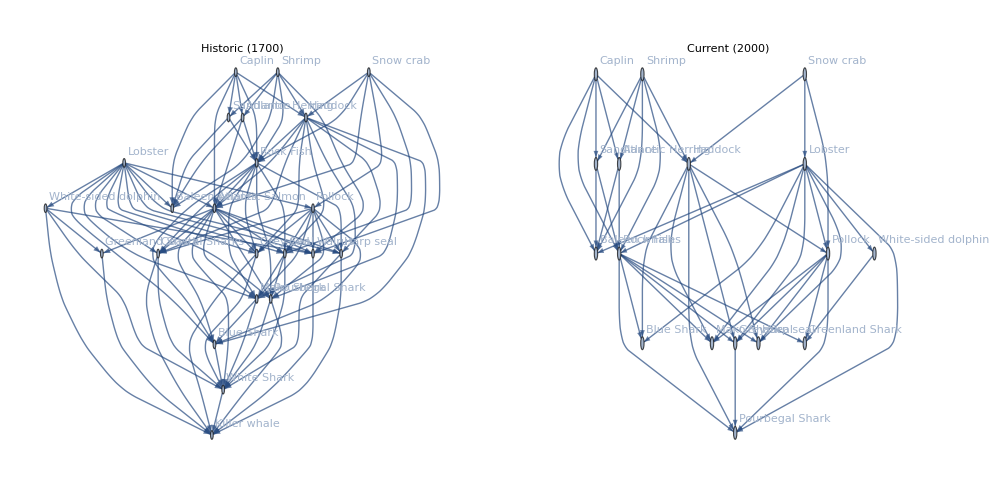

```mathematica
NetOut =Table[0,{l,1,2}];
Labels = {"Historic (1700)","Current (2000)"};
For[k=1,k<3,k++,
OccColumn = {4,6};
Occ = Delete[bodysize[[All,OccColumn[[k]]]],1];
Extinct =Position[Occ,0];
fwsize = Length[Position[Occ,1]];
BMmin = Delete[bodysize[[All,2]],1]; BMmin = Delete[BMmin,Extinct];
BMmax = Delete[bodysize[[All,3]],1]; BMmax = Delete[BMmax,Extinct];
BMavg = N[Mean[{BMmin,BMmax}]];
Spp = Delete[fmatrix[[1,All]],1];(*This gets rid of the label*) Spp = Delete[Spp,Extinct];(*This gets rid of the extinct species*)
f = fmatrix[[2;;Length[fmatrix],2;;Length[fmatrix]]];
f = Delete[f,Extinct];
f = Transpose[Delete[Transpose[f],Extinct]];
PRint = Table[
p = Exp[α + β*Log[BMavg[[j]]/BMavg[[i]]] + γ*Log[BMavg[[j]]/BMavg[[i]]]^2 + f[[i,j]]];
p/(1+p),
{i,1,fwsize},
{j,1,fwsize}
];
fw = Table[
If[i<j,
rv = RandomReal[];
If[
rv < PRint[[i,j]],
1,0],
0],
{i,1,fwsize},
{j,1,fwsize}
];
NetOut[[k]]=AdjacencyGraph[
Transpose[fw],VertexLabels->Table[i->Spp[[i]],{i,1,fwsize}],PlotLabel->Labels[[k]]]
]
GG =GraphicsGrid[{NetOut},ImageSize->1000]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/FigureNet.PDF",GG]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/FigureNet.PDF

```mathematica
MassValues = Table[10^i,{i,0,4,0.01}]
```

{1.,1.02329,1.04713,1.07152,1.09648,1.12202,1.14815,1.1749,1.20226,1.23027,1.25893,1.28825,1.31826,1.34896,1.38038,1.41254,1.44544,1.47911,1.51356,1.54882,1.58489,1.62181,1.65959,1.69824,1.7378,1.77828,1.8197,1.86209,1.90546,1.94984,1.99526,2.04174,2.0893,2.13796,2.18776,2.23872,2.29087,2.34423,2.39883,2.45471,2.51189,2.5704,2.63027,2.69153,2.75423,2.81838,2.88403,2.95121,3.01995,3.0903,3.16228,3.23594,3.31131,3.38844,3.46737,3.54813,3.63078,3.71535,3.80189,3.89045,3.98107,4.0738,4.16869,4.2658,4.36516,4.46684,4.57088,4.67735,4.7863,4.89779,5.01187,5.12861,5.24807,5.37032,5.49541,5.62341,5.7544,5.88844,6.0256,6.16595,6.30957,6.45654,6.60693,6.76083,6.91831,7.07946,7.24436,7.4131,7.58578,7.76247,7.94328,8.12831,8.31764,8.51138,8.70964,8.91251,9.12011,9.33254,9.54993,9.77237,10.,10.2329,10.4713,10.7152,10.9648,11.2202,11.4815,11.749,12.0226,12.3027,12.5893,12.8825,13.1826,13.4896,13.8038,14.1254,14.4544,14.7911,15.1356,15.4882,15.8489,16.2181,16.5959,16.9824,17.378,17.7828,18.197,18.6209,19.0546,19.4984,19.9526,20.4174,20.893,21.3796,21.8776,22.3872,22.9087,23.4423,23.9883,24.5471,25.1189,25.704,26.3027,26.9153,27.5423,28.1838,28.8403,29.5121,30.1995,30.903,31.6228,32.3594,33.1131,33.8844,34.6737,35.4813,36.3078,37.1535,38.0189,38.9045,39.8107,40.738,41.6869,42.658,43.6516,44.6684,45.7088,46.7735,47.863,48.9779,50.1187,51.2861,52.4807,53.7032,54.9541,56.2341,57.544,58.8844,60.256,61.6595,63.0957,64.5654,66.0693,67.6083,69.1831,70.7946,72.4436,74.131,75.8578,77.6247,79.4328,81.2831,83.1764,85.1138,87.0964,89.1251,91.2011,93.3254,95.4993,97.7237,100.,102.329,104.713,107.152,109.648,112.202,114.815,117.49,120.226,123.027,125.893,128.825,131.826,134.896,138.038,141.254,144.544,147.911,151.356,154.882,158.489,162.181,165.959,169.824,173.78,177.828,181.97,186.209,190.546,194.984,199.526,204.174,208.93,213.796,218.776,223.872,229.087,234.423,239.883,245.471,251.189,257.04,263.027,269.153,275.423,281.838,288.403,295.121,301.995,309.03,316.228,323.594,331.131,338.844,346.737,354.813,363.078,371.535,380.189,389.045,398.107,407.38,416.869,426.58,436.516,446.684,457.088,467.735,478.63,489.779,501.187,512.861,524.807,537.032,549.541,562.341,575.44,588.844,602.56,616.595,630.957,645.654,660.693,676.083,691.831,707.946,724.436,741.31,758.578,776.247,794.328,812.831,831.764,851.138,870.964,891.251,912.011,933.254,954.993,977.237,1000.,1023.29,1047.13,1071.52,1096.48,1122.02,1148.15,1174.9,1202.26,1230.27,1258.93,1288.25,1318.26,1348.96,1380.38,1412.54,1445.44,1479.11,1513.56,1548.82,1584.89,1621.81,1659.59,1698.24,1737.8,1778.28,1819.7,1862.09,1905.46,1949.84,1995.26,2041.74,2089.3,2137.96,2187.76,2238.72,2290.87,2344.23,2398.83,2454.71,2511.89,2570.4,2630.27,2691.53,2754.23,2818.38,2884.03,2951.21,3019.95,3090.3,3162.28,3235.94,3311.31,3388.44,3467.37,3548.13,3630.78,3715.35,3801.89,3890.45,3981.07,4073.8,4168.69,4265.8,4365.16,4466.84,4570.88,4677.35,4786.3,4897.79,5011.87,5128.61,5248.07,5370.32,5495.41,5623.41,5754.4,5888.44,6025.6,6165.95,6309.57,6456.54,6606.93,6760.83,6918.31,7079.46,7244.36,7413.1,7585.78,7762.47,7943.28,8128.31,8317.64,8511.38,8709.64,8912.51,9120.11,9332.54,9549.93,9772.37,10000.}

```mathematica
data = Flatten[Table[
p = Exp[alpha + beta*Log[PreyMass/PredMass] + gamma*Log[PreyMass/PredMass]^2]/.{alpha -> -2.61,beta -> -5.28,gamma -> -0.97};
{PreyMass,PredMass, p/(1+p)},
{PreyMass,MassValues},{PredMass,MassValues}],1];
```

```mathematica
LDP=ListDensityPlot[data,FrameLabel->{"Prey Mass","Predator Mass"},PlotLegends->BarLegend[{Automatic,{0,1}},LegendMarkerSize->180,LegendLabel->"Pr(link)"],ImageSize->250]
```

-Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/FigureProbLink.jpg",LDP,ImageResolution->600]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_HistoricOcean/OceanFoodWebs/FigureProbLink.jpg

```mathematica
ListDensityPlot[MapAt[Log,data,{All, ;;2}],Mesh->None,PlotRange->{{Log@(1),Log@10000},{Log@(1),Log@(10000)}},InterpolationOrder->3,PlotRange->{0,1}, FrameLabel->{"Prey mass","Predator mass"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(link)"]]
```

-Graphics-

```mathematica
Spp
```

{White Shark,Blue Shark,Mako Shark,Pourbegal Shark,Coastal Sharks,Cod,Greenland Shark,Sandlance,Atlantic Herring,Pollock ,Haddock,White-sided dolphin,Caplin,Shrimp,Lobster,Snow crab}

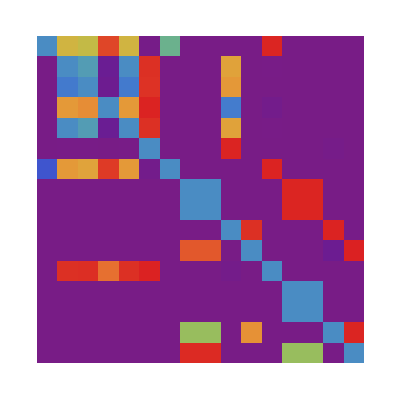

```mathematica
ArrayPlot[PRint,ColorFunction->"Rainbow"]
```

```mathematica
f
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}